```mathematica
(* Efective action 
 row and columns form 
EXTRA DIM RUNNING FASTEST?
theta_{\mu, s}

        th_x_1      th_y_1   th_x_2     th_y_2
   
th_x_1

th_y_1, 

th_x_2, 

th_y_2

*)
```

```mathematica
kh[k_] =  Exp[i k] -1
kc[k_]  = Exp[-i k]  - 1
```

-1+ⅇ^(i k)

-1+ⅇ^(-i k)

```mathematica
kkabs [k_] :=  2-2 Cos[ k]
kxy[kx_,ky_] := 1 - Cos[kx] - Cos[ky] + Cos[kx - ky]  
kxycom[kx_,ky_]= (Cos[ kx] + I Sin[kx] -1) (Cos[ ky] - I Sin[ky] -1)
```

(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky])

```mathematica
GEterm={{ 1,0,-1,0},
                { 0,1,0,-1},
                { -1,0, 1,0},
                {0,-1,0 ,1}}
```

{{1,0,-1,0},{0,1,0,-1},{-1,0,1,0},{0,-1,0,1}}

```mathematica
MatrixForm[GEterm]
```

(1 | 0 | -1 | 0
0 | 1 | 0 | -1
-1 | 0 | 1 | 0
0 | -1 | 0 | 1)

```mathematica
MatrixForm[GEterm]
```

(1 | 0 | -1 | 0
0 | 1 | 0 | -1
-1 | 0 | 1 | 0
0 | -1 | 0 | 1)

```mathematica
Mass = {{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}
```

{{1,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
MatrixForm[Mass]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
GBPlaq[kx_,ky_]  ={{   kkabs[ky]                            , -  kxy[kx,ky]                    },
                                  {   -  kxy[kx,ky]                           ,   kkabs[kx]                          }}
```

{{2-2 Cos[ky],-1+Cos[kx]-Cos[kx-ky]+Cos[ky]},{-1+Cos[kx]-Cos[kx-ky]+Cos[ky],2-2 Cos[kx]}}

```mathematica
GBPlaqH[kx_,ky_]  ={{   kkabs[ky]                            , -  kxycom[kx,ky]                 },
                                  {   -  kxycom[ky,kx]                           ,   kkabs[kx]                         }}
```

{{2-2 Cos[ky],-(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky])},{-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]),2-2 Cos[kx]}}

```mathematica
MatrixForm[{{2-2 Cos[ky],-(-1+ⅇ^(i kx)) (-1+ⅇ^(-i ky))},{-(-1+ⅇ^(-i kx)) (-1+ⅇ^(i ky)),2-2 Cos[kx]}}]
```

(2-2 Cos[ky] | (1-ⅇ^(i kx)) (-1+ⅇ^(-i ky))
(1-ⅇ^(-i kx)) (-1+ⅇ^(i ky)) | 2-2 Cos[kx])

```mathematica
GBterm[kx_,ky_] = ArrayFlatten[{{ GBPlaq[kx,ky],0},{ 0, GBPlaq[kx,ky]}}]
```

{{2-2 Cos[ky],-1+Cos[kx]-Cos[kx-ky]+Cos[ky],0,0},{-1+Cos[kx]-Cos[kx-ky]+Cos[ky],2-2 Cos[kx],0,0},{0,0,2-2 Cos[ky],-1+Cos[kx]-Cos[kx-ky]+Cos[ky]},{0,0,-1+Cos[kx]-Cos[kx-ky]+Cos[ky],2-2 Cos[kx]}}

```mathematica
Gmatrix[kx_,ky_] = GBterm[kx,ky] + GEterm + Mass
```

{{4-2 Cos[ky],-1+Cos[kx]-Cos[kx-ky]+Cos[ky],-1,0},{-1+Cos[kx]-Cos[kx-ky]+Cos[ky],4-2 Cos[kx],0,-1},{-1,0,3-2 Cos[ky],-1+Cos[kx]-Cos[kx-ky]+Cos[ky]},{0,-1,-1+Cos[kx]-Cos[kx-ky]+Cos[ky],3-2 Cos[kx]}}

```mathematica
MatrixForm[%14]
```

(4-2 Cos[ky] | -1+Cos[kx]-Cos[kx-ky]+Cos[ky] | -1 | 0
-1+Cos[kx]-Cos[kx-ky]+Cos[ky] | 4-2 Cos[kx] | 0 | -1
-1 | 0 | 3-2 Cos[ky] | -1+Cos[kx]-Cos[kx-ky]+Cos[ky]
0 | -1 | -1+Cos[kx]-Cos[kx-ky]+Cos[ky] | 3-2 Cos[kx])

```mathematica
Series[Gmatrix[kx,0],{kx,0,2}]
```

{{2,0,-1,0},{0,2+kx^2+O[kx]^3,0,-1},{-1,0,1,0},{0,-1,0,1+kx^2+O[kx]^3}}

```mathematica
GBtermH[kx_,ky_] = ArrayFlatten[{{ GBPlaqH[kx,ky],0},{ 0, GBPlaqH[kx,ky]}}]
```

{{2-2 Cos[ky],-(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky]),0,0},{-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]),2-2 Cos[kx],0,0},{0,0,2-2 Cos[ky],-(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky])},{0,0,-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]),2-2 Cos[kx]}}

```mathematica
MatrixForm[%16]
```

(2-2 Cos[ky] | -(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky]) | 0 | 0
-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]) | 2-2 Cos[kx] | 0 | 0
0 | 0 | 2-2 Cos[ky] | -(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky])
0 | 0 | -(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]) | 2-2 Cos[kx])

```mathematica
GmatrixH[kx_,ky_] = GBtermH[kx,ky] + GEterm + Mass
```

{{4-2 Cos[ky],-(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky]),-1,0},{-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]),4-2 Cos[kx],0,-1},{-1,0,3-2 Cos[ky],-(-1+Cos[kx]+ⅈ Sin[kx]) (-1+Cos[ky]-ⅈ Sin[ky])},{0,-1,-(-1+Cos[kx]-ⅈ Sin[kx]) (-1+Cos[ky]+ⅈ Sin[ky]),3-2 Cos[kx]}}

```mathematica
DetReal[kx_,ky_] = Expand[Det[GmatrixH[kx,ky]]]
```

95-90 Cos[kx]-5 Cos[kx]^2+10 Cos[kx]^3+Cos[kx]^4-90 Cos[ky]+40 Cos[kx] Cos[ky]+60 Cos[kx]^2 Cos[ky]-20 Cos[kx]^3 Cos[ky]-4 Cos[kx]^4 Cos[ky]-5 Cos[ky]^2+60 Cos[kx] Cos[ky]^2-63 Cos[kx]^2 Cos[ky]^2+6 Cos[kx]^3 Cos[ky]^2+6 Cos[kx]^4 Cos[ky]^2+10 Cos[ky]^3-20 Cos[kx] Cos[ky]^3+6 Cos[kx]^2 Cos[ky]^3+8 Cos[kx]^3 Cos[ky]^3-4 Cos[kx]^4 Cos[ky]^3+Cos[ky]^4-4 Cos[kx] Cos[ky]^4+6 Cos[kx]^2 Cos[ky]^4-4 Cos[kx]^3 Cos[ky]^4+Cos[kx]^4 Cos[ky]^4-25 Sin[kx]^2+10 Cos[kx] Sin[kx]^2+2 Cos[kx]^2 Sin[kx]^2+60 Cos[ky] Sin[kx]^2-20 Cos[kx] Cos[ky] Sin[kx]^2-8 Cos[kx]^2 Cos[ky] Sin[kx]^2-43 Cos[ky]^2 Sin[kx]^2+6 Cos[kx] Cos[ky]^2 Sin[kx]^2+12 Cos[kx]^2 Cos[ky]^2 Sin[kx]^2+6 Cos[ky]^3 Sin[kx]^2+8 Cos[kx] Cos[ky]^3 Sin[kx]^2-8 Cos[kx]^2 Cos[ky]^3 Sin[kx]^2+2 Cos[ky]^4 Sin[kx]^2-4 Cos[kx] Cos[ky]^4 Sin[kx]^2+2 Cos[kx]^2 Cos[ky]^4 Sin[kx]^2+Sin[kx]^4-4 Cos[ky] Sin[kx]^4+6 Cos[ky]^2 Sin[kx]^4-4 Cos[ky]^3 Sin[kx]^4+Cos[ky]^4 Sin[kx]^4-25 Sin[ky]^2+60 Cos[kx] Sin[ky]^2-43 Cos[kx]^2 Sin[ky]^2+6 Cos[kx]^3 Sin[ky]^2+2 Cos[kx]^4 Sin[ky]^2+10 Cos[ky] Sin[ky]^2-20 Cos[kx] Cos[ky] Sin[ky]^2+6 Cos[kx]^2 Cos[ky] Sin[ky]^2+8 Cos[kx]^3 Cos[ky] Sin[ky]^2-4 Cos[kx]^4 Cos[ky] Sin[ky]^2+2 Cos[ky]^2 Sin[ky]^2-8 Cos[kx] Cos[ky]^2 Sin[ky]^2+12 Cos[kx]^2 Cos[ky]^2 Sin[ky]^2-8 Cos[kx]^3 Cos[ky]^2 Sin[ky]^2+2 Cos[kx]^4 Cos[ky]^2 Sin[ky]^2-23 Sin[kx]^2 Sin[ky]^2+6 Cos[kx] Sin[kx]^2 Sin[ky]^2+4 Cos[kx]^2 Sin[kx]^2 Sin[ky]^2+6 Cos[ky] Sin[kx]^2 Sin[ky]^2+8 Cos[kx] Cos[ky] Sin[kx]^2 Sin[ky]^2-8 Cos[kx]^2 Cos[ky] Sin[kx]^2 Sin[ky]^2+4 Cos[ky]^2 Sin[kx]^2 Sin[ky]^2-8 Cos[kx] Cos[ky]^2 Sin[kx]^2 Sin[ky]^2+4 Cos[kx]^2 Cos[ky]^2 Sin[kx]^2 Sin[ky]^2+2 Sin[kx]^4 Sin[ky]^2-4 Cos[ky] Sin[kx]^4 Sin[ky]^2+2 Cos[ky]^2 Sin[kx]^4 Sin[ky]^2+Sin[ky]^4-4 Cos[kx] Sin[ky]^4+6 Cos[kx]^2 Sin[ky]^4-4 Cos[kx]^3 Sin[ky]^4+Cos[kx]^4 Sin[ky]^4+2 Sin[kx]^2 Sin[ky]^4-4 Cos[kx] Sin[kx]^2 Sin[ky]^4+2 Cos[kx]^2 Sin[kx]^2 Sin[ky]^4+Sin[kx]^4 Sin[ky]^4

```mathematica
Plot3D[DetReal[kx,ky],{kx,-Pi,Pi},{ky,-Pi,Pi}]
```

-Graphics3D-

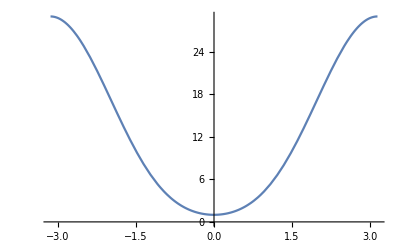

```mathematica
Plot[DetReal[kx,0],{kx,-Pi,Pi}]
```

```mathematica
Series[DetReal[kx,0],{kx,0,8}]
```

1+3 kx^2+(3 kx^4)/4-(19 kx^6)/120+(83 kx^8)/6720+O[kx]^9

```mathematica
DetReal8[kx_,ky_] =  Series[DetReal[kx,ky],{kx,0,8},{ky,0,8}]
```

(1+3 ky^2+(3 ky^4)/4-(19 ky^6)/120+(83 ky^8)/6720+O[ky]^9)+(3+2 ky^2-ky^4/6+ky^6/180-ky^8/10080+O[ky]^9) kx^2+(3/4-ky^2/6+ky^4/72-ky^6/2160+ky^8/120960+O[ky]^9) kx^4+(-19/120+ky^2/180-ky^4/2160+ky^6/64800-ky^8/3628800+O[ky]^9) kx^6+(83/6720-ky^2/10080+ky^4/120960-ky^6/3628800+ky^8/203212800+O[ky]^9) kx^8+O[kx]^9

```mathematica
Expand[GmatrixH[kx,ky]]
```

{{4-2 Cos[ky],-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky],-1,0},{-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky],4-2 Cos[kx],0,-1},{-1,0,3-2 Cos[ky],-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]},{0,-1,-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky],3-2 Cos[kx]}}

```mathematica
Meff[kx_,ky_] = {{Inverse[Expand[GmatrixH[kx,ky]]][[1]][[1]],Inverse[Expand[GmatrixH[kx,ky]]][[1]][[2]]},{Inverse[Expand[GmatrixH[kx,ky]]][[2]][[1]],Inverse[Expand[GmatrixH[kx,ky]]][[2]][[2]]}}
```

{{((11-14 Cos[kx]+4 Cos[kx]^2) (3-2 Cos[ky])-(4-2 Cos[kx]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]))/(-12+2 Cos[kx]-Cos[kx]^2+16 Cos[ky]-4 Cos[kx] Cos[ky]+2 Cos[kx]^2 Cos[ky]-5 Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2+(3-2 Cos[kx]) (-4+2 Cos[kx]+(3-2 Cos[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))-(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))),(-(3-2 Cos[kx]) (3-2 Cos[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky])+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-2 Cos[kx]+Cos[kx]^2-2 Cos[ky]+4 Cos[kx] Cos[ky]-2 Cos[kx]^2 Cos[ky]+Cos[ky]^2-2 Cos[kx] Cos[ky]^2+Cos[kx]^2 Cos[ky]^2+Sin[kx]^2-2 Cos[ky] Sin[kx]^2+Cos[ky]^2 Sin[kx]^2+Sin[ky]^2-2 Cos[kx] Sin[ky]^2+Cos[kx]^2 Sin[ky]^2+Sin[kx]^2 Sin[ky]^2))/(-12+2 Cos[kx]-Cos[kx]^2+16 Cos[ky]-4 Cos[kx] Cos[ky]+2 Cos[kx]^2 Cos[ky]-5 Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2+(3-2 Cos[kx]) (-4+2 Cos[kx]+(3-2 Cos[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))-(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2)))},{(-(3-2 Cos[kx]) (3-2 Cos[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky])+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-2 Cos[kx]+Cos[kx]^2-2 Cos[ky]+4 Cos[kx] Cos[ky]-2 Cos[kx]^2 Cos[ky]+Cos[ky]^2-2 Cos[kx] Cos[ky]^2+Cos[kx]^2 Cos[ky]^2+Sin[kx]^2-2 Cos[ky] Sin[kx]^2+Cos[ky]^2 Sin[kx]^2+Sin[ky]^2-2 Cos[kx] Sin[ky]^2+Cos[kx]^2 Sin[ky]^2+Sin[kx]^2 Sin[ky]^2))/(-12+2 Cos[kx]-Cos[kx]^2+16 Cos[ky]-4 Cos[kx] Cos[ky]+2 Cos[kx]^2 Cos[ky]-5 Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2+(3-2 Cos[kx]) (-4+2 Cos[kx]+(3-2 Cos[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))-(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))),((3-2 Cos[kx]) (11-14 Cos[ky]+4 Cos[ky]^2)-(4-2 Cos[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]))/(-12+2 Cos[kx]-Cos[kx]^2+16 Cos[ky]-4 Cos[kx] Cos[ky]+2 Cos[kx]^2 Cos[ky]-5 Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2+(3-2 Cos[kx]) (-4+2 Cos[kx]+(3-2 Cos[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2))-(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]-ⅈ Sin[kx]+ⅈ Cos[ky] Sin[kx]+ⅈ Sin[ky]-ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]+(-1+Cos[kx]+Cos[ky]-Cos[kx] Cos[ky]+ⅈ Sin[kx]-ⅈ Cos[ky] Sin[kx]-ⅈ Sin[ky]+ⅈ Cos[kx] Sin[ky]-Sin[kx] Sin[ky]) (15-6 Cos[kx]-Cos[kx]^2-6 Cos[ky]+2 Cos[kx]^2 Cos[ky]-Cos[ky]^2+2 Cos[kx] Cos[ky]^2-Cos[kx]^2 Cos[ky]^2-Sin[kx]^2+2 Cos[ky] Sin[kx]^2-Cos[ky]^2 Sin[kx]^2-Sin[ky]^2+2 Cos[kx] Sin[ky]^2-Cos[kx]^2 Sin[ky]^2-Sin[kx]^2 Sin[ky]^2)))}}

```mathematica
Simplify[Det[Expand[GmatrixH[kx,ky]]]]
```

33+2 Cos[2 kx]-22 Cos[ky]+Cos[kx] (-22+8 Cos[ky])+2 Cos[2 ky]

```mathematica
Nem[kx_,ky_] := Inverse[Expand[GmatrixH[kx,ky]]] *Simplify[Det[Expand[GmatrixH[kx,ky]]]]
```

```mathematica
MeffNum[kx_,ky_] := {{Nem[kx,ky][[1]][[1]],Nem[kx,ky][[1]][[2]]},{Nem[kx,ky][[2]][[1]],Nem[kx,ky][[2]][[2]]}}
```

```mathematica
Simplify[MeffNum[kx,ky]]
```

{{18+2 Cos[kx]^2+Cos[2 kx]-6 Cos[ky]+2 Cos[kx] (-9+2 Cos[ky]),-8 (-3+Cos[kx]+Cos[ky]) Sin[kx/2] (Cos[(kx-ky)/2]+ⅈ Sin[(kx-ky)/2]) Sin[ky/2]},{-8 (-3+Cos[kx]+Cos[ky]) Sin[kx/2] (Cos[(kx-ky)/2]-ⅈ Sin[(kx-ky)/2]) Sin[ky/2],19-18 Cos[ky]+Cos[kx] (-6+4 Cos[ky])+2 Cos[2 ky]}}

```mathematica
MatrixForm[%101]
```

%101

```mathematica
Eigenvalues[%102]
```

Eigenvalues[%102]

```mathematica
Eigenvalues[MeffNum[0,0]]
```

{1,1}

```mathematica
Eigenvectors[MeffNum[0,0]]
```

{{0,1},{1,0}}

```mathematica
Eigenvectors[MeffNum[1,-1]]//N
```

{{-0.540302-0.841471 ⅈ,1.},{0.540302+0.841471 ⅈ,1.}}

```mathematica
(* EffectiveAction[x_] := Integrate[ InverseG[kx,0][[1][[1]] Exp[ i kx x], {kx,-Pi,Pi}] *)
```